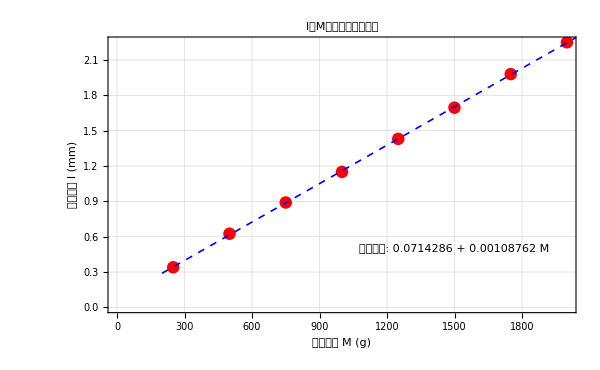

线性拟合方程: 0.0714286+0.00108762 M

斜率 k = 0.0714286 mm/g

截距 b = 0.00108762 mm

拟合优度 R.b2 = 0.999904

```mathematica
(*输入实验数据：{砝码质量M(g),平均长度l(mm)}*)data={{250,0.34},{500,0.625},{750,0.89},{1000,1.15},{1250,1.43},{1500,1.695},{1750,1.98},{2000,2.25}};

(*线性拟合：l=k*M+b*)
fit=LinearModelFit[data,M,M];
fitFunction=fit["Function"];  (*提取拟合函数*)

(*绘制散点图与拟合直线*)
Show[ListPlot[data,PlotStyle->{Red,PointSize[0.015]},(*数据点样式：红色圆点*)AxesLabel->{"砝码质量 M (g)","平均长度 l (mm)"},PlotLabel->"l随M的变化及线性拟合",GridLines->Automatic,Frame->True,LabelStyle->{FontSize->12}],Plot[fitFunction[M],{M,200,2100},(*拟合线范围略大于数据范围*)PlotStyle->{Blue,Dashed,Thickness[0.002]}  (*拟合线样式：蓝色虚线*)],ImageSize->600,Epilog->Text["拟合方程: "<>ToString[fit["BestFit"]],(*显示拟合方程*){1500,0.5},(*文本位置*)Background->White,FontSize->11]]

(*输出拟合参数*)
Print["线性拟合方程: ",fit["BestFit"]];
Print["斜率 k = ",fit["BestFitParameters"][[1]]," mm/g"];
Print["截距 b = ",fit["BestFitParameters"][[2]]," mm"];
Print["拟合优度 R.b2 = ",fit["RSquared"]];
```